```mathematica
(*This is the data which is used to denote the probability of a quantum jump occuring*)
data=Table[i,{i,0,1,.01}];
QJP=RandomChoice[data,1];
(*Next we must select the probability to select which collapse operator was responsible for said jump*)
CO=RandomChoice[data,1];
```

```mathematica
(*Initialization of the parameters for Decoherence*)
```

```mathematica
ω0=1;
Γ=6.069*10^-1(*Hz*)
```

0.6069

```mathematica
(*Normalized Time Evoltion of Population of a Two-Level Atom*)
```

```mathematica
c[τ_]:=Cos[ω0*τ]Exp[(-Γ*τ)/2]
```

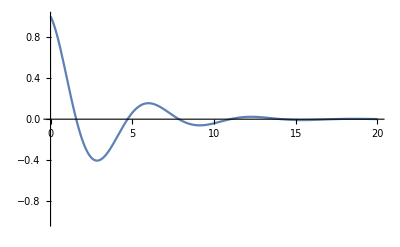

```mathematica
Plot[c[t],{t,0,20},PlotRange->{{0,20},{-1,1}}]
```